#### Notes

Maybe we can test random weights for some number of attempts then skip to next if none are found. This random search would reduce memory complexity of the algorithm. 
		First: Test random weights to reduce Graph List
	 	Second: Complete Test of all weights
	 	Third: ?
	
	Understanding the relationships between graphs would be nice. We could test the graphs in order of inclusion as a subgraph. So Construct a Poset of the graphs where the order is by inclusion as isomorphic subgraphs ( Not sure if this actually leads to a Poset structure but the idea is still there). Then perform tests according to the ordering.

#### Helper Functions

```mathematica
(*Helper Functions*)
PerfectDistanceQ[G_,w_]:=Union@*Flatten@*Round@GraphDistanceMatrix[Graph[G,EdgeWeight->w]] == Range[0,Binomial[VertexCount[G],2]];
WeightSets[Vn_,En_]:=Select[Subsets[Range[Binomial[Vn,2]],{En}],MemberQ[#,1]&&MemberQ[#,2]&] ;
ReduceWeightSets[W_,Vn_]:=Pick[W,Table[SubsetQ[(Total/@Subsets[W[[i]],Length[W[[i]]]]),Range[0,Binomial[Vn,2]]],{i,1,Length[W]}]]
ReduceWeightSetsDiam[W_,G_]:=Pick[W,Table[SubsetQ[(Total/@Subsets[W[[i]],GraphDiameter[G]]),Range[0,Binomial[VertexCount[G],2]]],{i,1,Length[W]}]]

TotalWeightings[G_] := EdgeCount[G]!Binomial[Binomial[VertexCount[G],2]-2,EdgeCount[G]-2];
StatusGraph[GraphList_,NPDG_,MPDG_]:=Module[{G,NPDGC,MPDGC},G =ResourceFunction["HasseDiagram"][IsomorphicSubgraphQ,CanonicalGraph/@GraphList];NPDGC=CanonicalGraph/@NPDG;MPDGC=CanonicalGraph/@MPDG; HighlightGraph[G,{Style[NPDGC,Red],Style[VertexOutComponent[G,MPDGC],Green],Style[MPDGC,Blue]},GraphLayout->"LayeredDigraphEmbedding",VertexLabels->MapIndexed[#->Placed[{VertexList[G][[#2[[1]]]]},{Tooltip}]&,VertexList[G]],EdgeStyle->Directive[Thin,Gray]]];
```

#### Code

```mathematica
MPDG = CanonicalGraph[#]&/@Import["/Users/alexanderhabib/MPDG7_Incomplete.mx"];
NPDG =CanonicalGraph[#]&/@Import["/Users/alexanderhabib/NPDG7_Incomplete.mx"];
(*Graphs = CanonicalGraph[#]&/@SortBy[Import["/Users/alexanderhabib/Desktop/Graphs/connected_graphs/n_7/graph7c.g6"],EdgeCount];*)
(*MinimalPerfectDistanceGraphs = MPDG;
NotPerfectDistanceGraphs = NPDG;

GraphList = Complement[Graphs,Union[NotPerfectDistanceGraphs,VertexOutComponent[ResourceFunction["HasseDiagram"][IsomorphicSubgraphQ,Graphs],MPDG]]];*)
```

Import::nffil: File /Users/alexanderhabib/MPDG7_Incomplete.mx not found during Import.

Import::nffil: File /Users/alexanderhabib/NPDG7_Incomplete.mx not found during Import.

```mathematica
Graphs = SortBy[Import["C:\\Users\\patri\\Desktop\\Graphs Research\\G6 Graphs\\Connected (By Vertices)\\graph7c.g6"], EdgeCount];
```

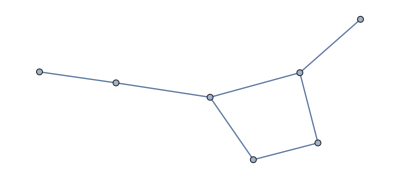
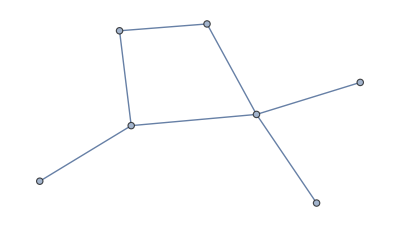
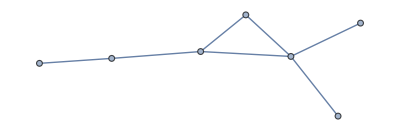
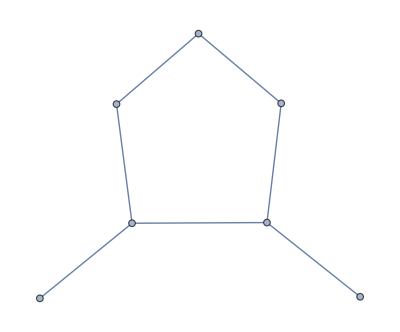
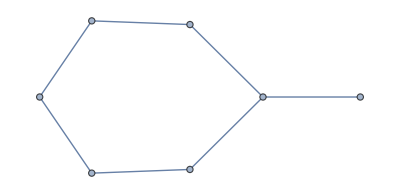
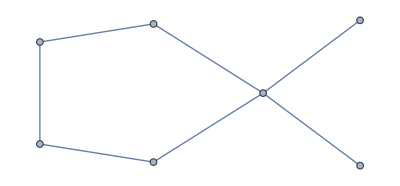
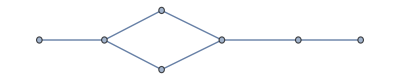
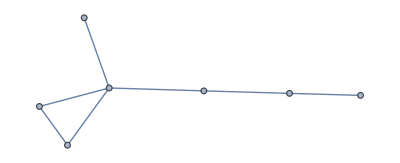
Time To Compute:	21:57:07TimeObject[{21,57,7.07055},Instant] and 70.5481ms
Minimal Perfect Distance Graphs(18): 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Not Perfect Distance Graphs(51): 
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

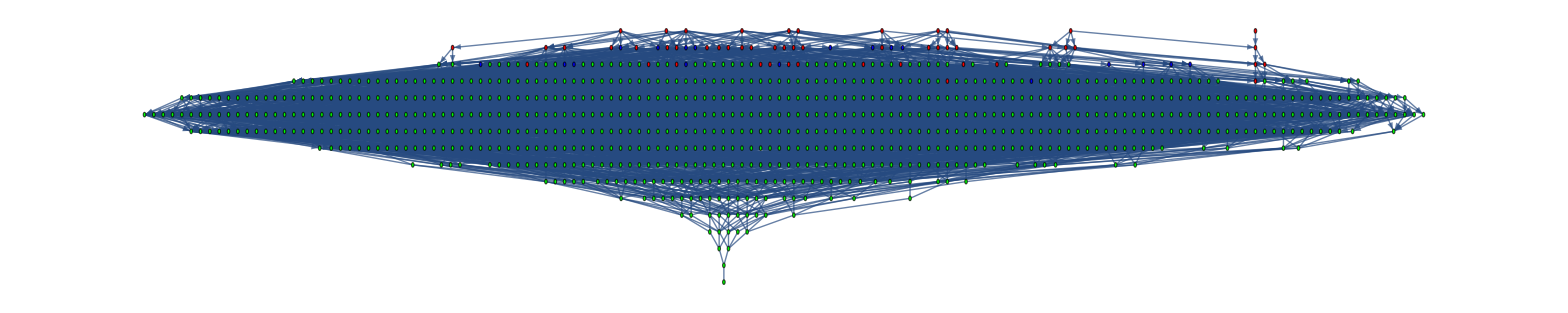

```mathematica
GraphList = Graphs;

MinimalPerfectDistanceGraphs = {}; NotPerfectDistanceGraphs = {};

TotalTime = AbsoluteTiming[
While[Length[GraphList]!=0,
GraphsGivenEdgeCount = First[GatherBy[GraphList,EdgeCount]];
VCount = VertexCount[GraphsGivenEdgeCount[[1]]];
ECount = EdgeCount[GraphsGivenEdgeCount[[1]]];

W = ReduceWeightSets[WeightSets[VCount ,ECount],VCount];

PDGs = {};
SetSharedVariable[PDGs];
DistributeDefinitions[PerfectDistanceQ,W];

ParallelDo[
PDGQ =Catch[Do[
WL = Permutations[Wi];ResWi =Catch[Do[If[PerfectDistanceQ[G,w],Throw[True]],{w,WL}]];If[ResWi===True,Throw[ResWi]];,{Wi,W}]];

If[PDGQ,AppendTo[PDGs,G]]
,{G,GraphsGivenEdgeCount},Method->"FinestGrained",DistributedContexts->None];

GraphList = Complement[GraphList,GraphsGivenEdgeCount];

Do[GraphList = Select[GraphList,Not[IsomorphicSubgraphQ[PDG,#]]&],{PDG,PDGs}];

Do[AppendTo[MinimalPerfectDistanceGraphs,PDG],{PDG,PDGs}];
Do[AppendTo[NotPerfectDistanceGraphs,PDG],{PDG,Complement[GraphsGivenEdgeCount,PDGs]}];

]][[1]];


Print[
"Time To Compute:\t",TimeObject[{0,0,TotalTime}]," and ",1000FractionalPart[TotalTime],"ms\n",
"Minimal Perfect Distance Graphs(",Length[MinimalPerfectDistanceGraphs],"): \n",TableForm[MinimalPerfectDistanceGraphs,TableDirections->Row],"\n",
"Not Perfect Distance Graphs(",Length[NotPerfectDistanceGraphs],"): \n",
TableForm[NotPerfectDistanceGraphs,TableDirections->Row]
]

StatusGraph[Graphs,NotPerfectDistanceGraphs,MinimalPerfectDistanceGraphs]
```